# Lists

Lesson: Listshttps://vimeo.com/ondemand/mathematica/729382903Nonehttps://vimeo.com/ondemand/mathematica/729382903HyperlinkActionRecycledHyperlinkActive
Course: Mathematica Essentials

## Introduction

```mathematica
primes={2,3,5,7,11,13,17}
```

{2,3,5,7,11,13,17}


{π,Hello world,-Graphics-,f[x]}

```mathematica
random={π, "Hello world",Graphics[ Circle[]],f[x]}
```

```mathematica
values=Table[x^2+3x-5,{x,-4,4}]
```

{-1,-5,-7,-7,-5,-1,5,13,23}

```mathematica
primes=Table[Prime[j],{j,10}]
```

{2,3,5,7,11,13,17,19,23,29}

```mathematica
odds=Table[n,{n,1,20,2}]
```

{1,3,5,7,9,11,13,15,17,19}

## Functions that use Lists as Arguments

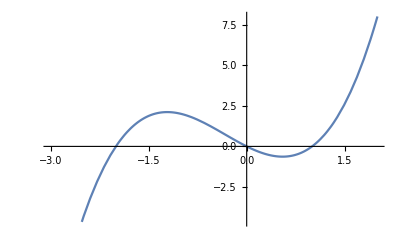

```mathematica
Plot[x^3+x^2-2x,{x,-3,2}]
```

```mathematica
Sum[x^3-5x,{x,-7,7}]
```

0

```mathematica
Table[x^3-5x,{x,-7,7}]
```

{-308,-186,-100,-44,-12,2,4,0,-4,-2,12,44,100,186,308}

```mathematica
Integrate[E^(-x^2/2),{x,-∞,∞}]
```

√(2 π)

## Extracting Parts of Lists

```mathematica
elements=ElementData[]
```

{hydrogen,helium,lithium,beryllium,boron,carbon,nitrogen,oxygen,fluorine,neon,sodium,magnesium,aluminum,silicon,phosphorus,sulfur,chlorine,argon,potassium,calcium,scandium,titanium,vanadium,chromium,manganese,iron,cobalt,nickel,copper,zinc,gallium,germanium,arsenic,selenium,bromine,krypton,rubidium,strontium,yttrium,zirconium,niobium,molybdenum,technetium,ruthenium,rhodium,palladium,silver,cadmium,indium,tin,antimony,tellurium,iodine,xenon,cesium,barium,lanthanum,cerium,praseodymium,neodymium,promethium,samarium,europium,gadolinium,terbium,dysprosium,holmium,erbium,thulium,ytterbium,lutetium,hafnium,tantalum,tungsten,rhenium,osmium,iridium,platinum,gold,mercury,thallium,lead,bismuth,polonium,astatine,radon,francium,radium,actinium,thorium,protactinium,uranium,neptunium,plutonium,americium,curium,berkelium,californium,einsteinium,fermium,mendelevium,nobelium,lawrencium,rutherfordium,dubnium,seaborgium,bohrium,hassium,meitnerium,darmstadtium,roentgenium,copernicium,nihonium,flerovium,moscovium,livermorium,tennessine,oganesson}

```mathematica
Length[elements]
```

118

```mathematica
First[elements]
```

hydrogen

```mathematica
Last[elements]
```

oganesson

```mathematica
elements[[8]]
```

oxygen

```mathematica
elements[[{8,20,92}]]
```

{oxygen,calcium,uranium}

```mathematica
Take[elements,10]
```

{hydrogen,helium,lithium,beryllium,boron,carbon,nitrogen,oxygen,fluorine,neon}

```mathematica
Take[elements,-10]
```

{meitnerium,darmstadtium,roentgenium,copernicium,nihonium,flerovium,moscovium,livermorium,tennessine,oganesson}

```mathematica
Take[elements,{10,20}]
```

{neon,sodium,magnesium,aluminum,silicon,phosphorus,sulfur,chlorine,argon,potassium,calcium}

```mathematica
Select[elements,#["HalfLife"] <Quantity[1, "Years"]&]
```

{astatine,radon,francium,fermium,mendelevium,nobelium,lawrencium,rutherfordium,dubnium,seaborgium,bohrium,hassium,meitnerium,darmstadtium,roentgenium,copernicium,nihonium,flerovium,moscovium,livermorium,tennessine,oganesson}

## Common List Operations

```mathematica
socratica={"s","o","c","r","a","t","i","c","a"};
mathematica=Characters["mathematica"];
```

```mathematica
socratica
```

{s,o,c,r,a,t,i,c,a}

```mathematica
mathematica
```

{m,a,t,h,e,m,a,t,i,c,a}

```mathematica
Join[socratica,mathematica]  (* Concatenate the two lists *)
```

{s,o,c,r,a,t,i,c,a,m,a,t,h,e,m,a,t,i,c,a}

```mathematica
Union[socratica,mathematica]  (* Take the union of the two lists *)
```

{a,c,e,h,i,m,o,r,s,t}

```mathematica
mathematica∪socratica  (* [esc] un [esc] ]*)
```

{a,c,e,h,i,m,o,r,s,t}

```mathematica
Union[socratica]  (* Convert list into an ordered set *)
```

{a,c,i,o,r,s,t}

```mathematica
Append[Union[socratica], "a"]
```

{a,c,i,o,r,s,t,a}

```mathematica
Union[%]
```

{a,c,i,o,r,s,t}

```mathematica
Intersection[socratica,mathematica]
```

{a,c,i,t}

```mathematica
socratica∩mathematica  (* [esc] i-n-t-e-r [esc] *)
```

{a,c,i,t}

## Vectors

```mathematica
v1={3,5};
v2={5,-3};
```

```mathematica
v1+v2
```

{8,2}

```mathematica
v1.v2
```

0

```mathematica
2v1
```

{6,10}

```mathematica
VectorAngle[v1,v2]
```

π/2

```mathematica
w1={1,4,-3};
w2={2,0,7};
Cross[w1,w2]
```

{28,-13,-8}

```mathematica
z={1,4,-2,0.5}
```

{1,4,-2,0.5}

## Matrices

```mathematica
m={{2,5},{1,3}}
```

{{2,5},{1,3}}

```mathematica
MatrixForm[m]
```

(2 | 5
1 | 3)

```mathematica
Det[m]
```

1

```mathematica
MatrixPower[m,-1]
```

{{3,-5},{-1,2}}

```mathematica
m.{x,y}
```

{2 x+5 y,x+3 y}

```mathematica
Solve[m.{x,y}=={5,2}]
```

{{x→5,y→-1}}

## Lists as Expressions

```mathematica
v={π,3}
```

{π,3}

```mathematica
FullForm[v]
```

List[Pi,3]

```mathematica
v[[1]]
```

π

```mathematica
v[[2]]
```

3

```mathematica
v[[0]]
```

List